```mathematica
(*Transforma tensor vetorial de voigth em tensor  3x3*)
FromVoigtToCart[sig_]:={{sig[[1]],sig[[6]],sig[[5]]},{sig[[6]],sig[[2]],sig[[4]]},{sig[[5]],sig[[4]],sig[[3]]}}
(*Transforma tensor  3x3 em tensor vetorial de voigth *)
FromCartToVoigt[sig_]:={sig[[1,1]],sig[[2,2]],sig[[3,3]],sig[[2,3]],sig[[1,3]],sig[[1,2]]}
FromCartToVoigt2[sig_]:={sig[[1,1]],sig[[2,2]],sig[[3,3]],2sig[[2,3]],2sig[[1,3]],2sig[[1,2]]}
ComputeS[m_]:=Block[{cart,Sint},
cart=FromVoigtToCart[m];
Sint=cart-1/3 Tr[cart]IdentityMatrix[3];
FromCartToVoigt2[Sint]
]
ComputeS2[m_]:=Block[{cart,Sint},
cart=FromVoigtToCart[m];
Sint=cart-1/3 Tr[cart]IdentityMatrix[3];
FromCartToVoigt[Sint]
]
ComputeJ2[m_]:=Block[{cart,S},
cart=FromVoigtToCart[m];
S=cart-1/3 Tr[cart]IdentityMatrix[3];
1/2. Tr[S.S]
]
ComputeI1[m_]:=Block[{cart,S},
cart=FromVoigtToCart[m];
N[Tr[cart]]
]
P={{2/3,-1/3,-1/3,0,0,0},{-1/3,2/3,-1/3,0,0,0},{-1/3,-1/3,2/3,0,0,0},{0,0,0,2,0,0},{0,0,0,0,2,0},{0,0,0,0,0,2}};
Ii={1,1,1,0,0,0};
Clear[a,b]
(*ax[sigma_]:=(-4apex b^2 Ii+4/3 b^2 ComputeI1[sigma] Ii - 6 a^2 ComputeS[sigma]) /(6 a^2 b^2)
dadsigmax[sigma_]:=(-6 a^2 P +4/3 b^2 Outer[Times,Ii,Ii])/(6 a^2 b^2)*)
ax[sigma_]:=(6 apex b^2 Ii-2 b^2 ComputeI1[sigma]Ii+9 a^2 ComputeS[sigma])/(9 a^2 b^2)//.subst2
dadsigmax[sigma_]:=(P/b^2)-(2 Outer[Times,Ii,Ii]/(9 a^2))//.subst2

(*ax[sigma_]:=a/3 {1,1,1,0,0,0}+1/(2Sqrt[ComputeJ2[sigma]])ComputeS[sigma]
dadsigmax[sigma_]:=P 1/(2 Sqrt[ComputeJ2[sigma]])-1/(4 ComputeJ2[sigma]^(3/2))Outer[Times,ComputeS[sigma],ComputeS[sigma]]*)

(*Calcula autovalores e autovetores e ordena na ordem decrescente*)
EigenSystem[m_]:=Block[{epstprincipalvals,epstprincipaldir,orderedvalues,index,oderedvectors,cart},
cart=FromVoigtToCart[m];
{epstprincipalvals,epstprincipaldir}=Eigensystem[cart//N];
orderedvalues=Sort[epstprincipalvals,Greater];
index=DeleteDuplicates[Table[Position[epstprincipalvals,orderedvalues[[i]]],{i,1,3}]//Flatten];
oderedvectors=Table[epstprincipaldir[[index[[i]]]],{i,1,3}];
{orderedvalues,oderedvectors}
]
HW[{xi_,rho_,beta_}]:=Block[{sig1,sig2,sig3},
sig1=xi /Sqrt[3]+Sqrt[2/3]rho Cos[beta];
sig2=xi/Sqrt[3] +Sqrt[2/3]rho Cos[beta-2Pi/3];
sig3=xi/Sqrt[3] +Sqrt[2/3] rho Cos[beta+2Pi/3];
N[{sig1,sig2,sig3}]
];

F1HWCylDruckerPrager[{xi_,rho_,beta_}]:=Block[{xiint,rhoint,betaint,sigy,a,b,c,apex},
xiint=xi;
rhoint=(-3 √2 apex b+√6 b xi)/(3 a);
betaint=beta;
N[{xiint,rhoint,betaint}]
];


F1HWCylDruckerPragerSmoothPSMATCH[{xi_,rho_,beta_}]:=Block[{tanpsi,xiint,rhoint,betaint,sigy,a,b,c,phi,fht,apex},
xiint=If[xi>apex,apex,xi];
rhoint=Sqrt[-(2 b^2 (3 a^2-3 apex^2+2 √3 apex xiint-xiint^2))/(3 a^2)];
betaint=beta;
{xiint,rhoint,betaint}
]
DistFuncEnergy[pt_,xi_,rho_,beta_,F_]:=Block[{EM,young,diff,C,parametrictrial,parametric,x,p1,y,p2,z,p3,distf1,sig,sigtrial,sigHW,sig2,sig3,sig1tr,sig2tr,sig3tr,haigh,haightrial,G,K,Rot},
Rot=({{1/(√3), 1/(√3), 1/(√3)}, {√(2/3), -1/(√6), -1/(√6)}, {0, 1/(√2), -1/(√2)}});
parametric=F1HWCart[xi ,rho ,beta,F];
parametrictrial=Rot.pt;
EM={{Sqrt[young/(3K)],0,0},{0,Sqrt[young/(2G)],0},{0,0,Sqrt[young/(2G)]}};
diff=EM.(parametrictrial-parametric);

distf1= Sqrt[1/young(diff.diff)];
Return[distf1]
];
F1HWCart[xi_,rho_,beta_,F_]:=Block[{temp},
temp=F[{xi,rho,beta}];
{temp[[1]],Cos[temp[[3]]]temp[[2]],Sin[temp[[3]]]temp[[2]]}
]

(*Dado a tensão trial, os valores numéricos das constantes materiais, e a equação parametrica da superfíe plástica, encontra numericamente os valores que minimizam a distancia no espaço das deformações que são solução do problema plástico*)
numericalsolution[sigma_,data_,parametricyieldsurface_,fDist_]:=Block[{tab,index,xisol,dist,xi,rho,betasol,xiguess,betaguess,distxi,distnew,ξn,βn,res,pt,sig1,sig2,sig3},

pt=EigenSystem[sigma][[1]]//N;
betasol=betafunc[pt];
(*dist=(fDist[pt,xi,rho,betasol,parametricyieldsurface]^2)//.data;*)
dist=distfuncenergy[pt,betasol]//.subst2;
ξn=(pt[[1]]+pt[[2]]+pt[[3]])/Sqrt[3];
pt1=-50. ξn;
pt2=50.ξn;
tab=Table[{var,dist/.xi->var},{var,pt1,pt2,(pt2-pt1)/10000.}];
(*Print[Min[Transpose[tab][[2]]]];*)
index=Position[tab,Min[Transpose[tab][[2]]]];
(*Print["index = ",index];
Print["tab[[index[[1]] ]] = ",tab[[index[[1,1]] ]][[1]]];
Print["tab = ",tab];*)
res=D[dist,xi];
ξn=tab[[index[[1,1]] ]][[1]];
xisol=FindRoot[res,{xi,ξn}][[1,2]];
{xisol,betasol}
]
betafunc[{sig1_,sig2_,sig3_}]:=ArcTan[(√3.00001 (-sig2+sig3))/(-2.00001 sig1+sig2+sig3)]
(*FDP[I1_,J2_]:=(Sqrt[J2]+A I1/3 -c B)*)
phidp[xi_,rho_]:=-(((apex-If[xi>=apex, apex ,xi]/Sqrt[3])/a)^2 -((rho/Sqrt[2])/b)^2 -1)//.subst2;
cc=1;
distfuncenergy[{sig1_,sig2_,sig3_},beta_]:=1/108 ((4 (√3 (sig1+sig2+sig3)-3 If[xi>apex,apex,xi])^2)/K+(9 (-2 sig1+sig2+sig3+2 Cos[beta] √((b^2 (-3 a^2+3 apex^2-2 √3 apex If[xi>apex,apex,xi]+If[xi>apex,apex,xi]^2))/a^2))^2)/G+(3 (-3 sig2+3 sig3+2 √3 √((b^2 (-3 a^2+3 apex^2-2 √3 apex If[xi>apex,apex,xi]+If[xi>apex,apex,xi]^2))/a^2) Sin[beta])^2)/G)//N;
distfuncenergyDP[{sig1_,sig2_,sig3_},beta_]:=(8 a^2 G (√3 sig1+√3 sig2+√3 sig3-3 xi)^2+6 K (√3 a (2 sig1-sig2-sig3)+2 b (3 apex-√3 xi) Cos[beta])^2+6 K (3 a (sig2-sig3)+2 b (3 apex-√3 xi) Sin[beta])^2)/(216 a^2 G K);
ddist[{sig1_,sig2_,sig3_},beta_]:=1/108 (-(24 If[xi>apex,0,1] (√3 (sig1+sig2+sig3)-3 If[xi>apex,apex,xi]))/K+(18 b^2 Cos[beta] (-2 √3 apex If[xi>apex,0,1]+2 If[xi>apex,0,1] If[xi>apex,apex,xi]) (-2 sig1+sig2+sig3+2 Cos[beta] √((b^2 (-3 a^2+3 apex^2-2 √3 apex If[xi>apex,apex,xi]+If[xi>apex,apex,xi]^2))/a^2)))/(a^2 G √((b^2 (-3 a^2+3 apex^2-2 √3 apex If[xi>apex,apex,xi]+If[xi>apex,apex,xi]^2))/a^2))+(6 √3 b^2 (-2 √3 apex If[xi>apex,0,1]+2 If[xi>apex,0,1] If[xi>apex,apex,xi]) Sin[beta] (-3 sig2+3 sig3+2 √3 √((b^2 (-3 a^2+3 apex^2-2 √3 apex If[xi>apex,apex,xi]+If[xi>apex,apex,xi]^2))/a^2) Sin[beta]))/(a^2 G √((b^2 (-3 a^2+3 apex^2-2 √3 apex If[xi>apex,apex,xi]+If[xi>apex,apex,xi]^2))/a^2)))//N;
numericalsolution[pt_]:=Block[{tab,index,xisol,dist,xi,rho,betasol,xiguess,betaguess,distxi,distnew,ξn,βn,res,sig1,sig2,sig3},

betasol=betafunc[pt];
ξn=(pt[[1]]+pt[[2]]+pt[[3]])/Sqrt[3.];
res=ddist[pt,betasol]//.subst2;
xisol=FindRoot[res,{xi,0}][[1,2]];
{xisol,betasol}
];
Optimization`NMinimizeDump`$Methods
(* ->{Automatic,DifferentialEvolution,NelderMead,SimulatedAnnealing,RandomSearch,NonlinearInteriorPoint}*)
ApplyStrainComputeSigmaDep[epst_,epsp_,subst2_]:=Block[{distsmooth,dist,solnum,H,AA,Dd,sepstrial,AFACT,BFACT,CFACT,DFACT,Is,ETDNOR,invCe,R,Q,invQ,sig1,sig2,sig3,epse2D,sz,nu,ex,ey,exy,sx,sy,tauxy,sigproj2D,Dep2D,sn1,pn1,updatedstress,II,eq,c ,B,A,solgamma,full,dgamma,acone,yield,I1,J2,sol,d,Dep,CT,T,epse,gamma,epsetrial,sigprojvoigth,proj,asol,dadsigg,THWR,Rot,xitrial,xisol,xi,beta,rho,sigma,rhotrial,Ce,pt,vec,betasol,young,G,K,epstint,epspint},

Ce=N[{{(4 G)/3+K,-(2 G)/3+K,-(2 G)/3+K,0,0,0},{-(2 G)/3+K,(4 G)/3+K,-(2 G)/3+K,0,0,0},{-(2 G)/3+K,-(2 G)/3+K,(4 G)/3+K,0,0,0},{0,0,0,G,0,0},{0,0,0,0,G,0},{0,0,0,0,0,G}}]//.subst2;
invCe=N[{{(G+3 K)/(9 G K),-1/(6 G)+1/(9 K),-1/(6 G)+1/(9 K),0,0,0},{-1/(6 G)+1/(9 K),(G+3 K)/(9 G K),-1/(6 G)+1/(9 K),0,0,0},{-1/(6 G)+1/(9 K),-1/(6 G)+1/(9 K),(G+3 K)/(9 G K),0,0,0},{0,0,0,1/G,0,0},{0,0,0,0,1/G,0},{0,0,0,0,0,1/G}}]//.subst2;

epstint={epst[[1]],epst[[2]],0,0,0,epst[[3]]}//N;
epspint={epsp[[1]],epsp[[2]],0,0,0,epsp[[3]]}//N;

epsetrial=(epstint-epspint);

sigma=Ce.epsetrial;


If[MatchQ[sigma[[1]],_Complex]==True||MatchQ[sigma[[2]],_Complex]==True  || MatchQ[sigma[[3]],_Complex]==True||MatchQ[sigma[[4]],_Complex]==True||MatchQ[sigma[[5]],_Complex]==True  || MatchQ[sigma[[6]],_Complex]==True,
Print["sigma = ",sigma];
Print["epstint = ",epstint];
Print["epspint = ",epspint];
Break[];
];

I1=ComputeI1[sigma];
J2=ComputeJ2[sigma];
yield=phidp[I1/Sqrt[3],Sqrt[2J2]]//.subst2;


If[yield<0,
sigprojvoigth=sigma;
epse=epsetrial;
Dep=Ce;
gamma=0;
,

xitrial=I1/Sqrt[3];
rhotrial=Sqrt[2J2];

(*Auto valores em ordem decrescente*)
{pt,vec}=EigenSystem[sigma]//N;

betasol=betafunc[pt];
distsmooth=distfuncenergy[pt,betasol]//.subst2;
(*distsmooth=distfuncenergyDP[pt,betasol]//.subst2;*)
(*{dist,xisol}=NMinimize[distsmooth,xi,Method->{"DifferentialEvolution","ScalingFactor"->1.,"CrossProbability"->0.5, "ScalingFactor"->1.}];*)
{dist,xisol}=NMinimize[distsmooth,xi,Method->{"SimulatedAnnealing","PerturbationScale"->3}];
xisol=xisol[[1,2]];

(*{xisol,betasol}=numericalsolution[pt];*)

proj=HW[F1HWCylDruckerPragerSmoothPSMATCH[{xisol,rho,betasol}]]//.subst2;


If[MatchQ[proj[[1]],_Complex]==True||MatchQ[proj[[2]],_Complex]==True  || MatchQ[proj[[3]],_Complex]==True,
proj=HW[{apex,0,0}]//.subst2;
Dep=Ce 0;
sigprojvoigth=FromCartToVoigt[Sum[proj[[i]] Outer[Times,vec[[i]],vec[[i]]],{i,1,3}]];
gamma=0;
,
sigprojvoigth=FromCartToVoigt[Sum[proj[[i]] Outer[Times,vec[[i]],vec[[i]]],{i,1,3}]];
asol=ax[sigprojvoigth]//.subst2;
dadsigg=dadsigmax[sigprojvoigth]//.subst2;
epse=invCe.sigprojvoigth;
gamma=Norm[epsetrial-epse]/Norm[asol];


Q=(IdentityMatrix[6]+gamma Ce.dadsigg);
R=Inverse[Q].Ce;
Dep= R-1/(asol.R.asol) Outer[Times,R.asol,R.asol];


];


];

If[MatchQ[sigprojvoigth[[1]],_Complex]==True||MatchQ[sigprojvoigth[[2]],_Complex]==True  || MatchQ[sigprojvoigth[[3]],_Complex]==True||MatchQ[sigprojvoigth[[4]],_Complex]==True||MatchQ[sigprojvoigth[[5]],_Complex]==True  || MatchQ[sigprojvoigth[[6]],_Complex]==True,
Print["sigprojvoigth = ",sigprojvoigth];
Print["vec = ",vec];
Print["pt = ",pt];
Break[];
];
Dep2D={{Dep[[1,1]],Dep[[1,2]],Dep[[1,6]]},{Dep[[2,1]],Dep[[2,2]],Dep[[2,6]]},{Dep[[6,1]],Dep[[6,2]],Dep[[6,6]]}};
sigproj2D={sigprojvoigth[[1]],sigprojvoigth[[2]],sigprojvoigth[[6]]};
{sx,sy,tauxy}=sigproj2D;
sz=nu(sx+sy);
ex=1/young (sx-nu(sy+sz));
ey=1/young (sy-nu(sx+sz));
exy=tauxy/(G);
epse2D={ex,ey,exy};
{sigproj2D,Dep2D,epse2D,gamma}//.subst2

];
(*Compute2DShape*)
Compute2DShape[order_,eltype_]:=Block[{zeta1,zeta2,zeta3,a,b,xi,eta,psis,dpsis},
If[serendipity==True,
psis={
(1-xi)(1-eta)(-xi-eta-1)/4,(*1*)(1+xi)(1-eta)(xi-eta-1)/4,(*2*)(1+xi)(1+eta)(xi+eta-1)/4,(*3*)(1-xi)(1+eta)(-xi+eta-1)/4,(*4*)
(1-xi^2)(1-eta)/2,(*5*)(1+xi)(1-eta^2)/2,(*6*)(1-xi^2)(1+eta)/2,(*7*)(1-xi)(1-eta^2)/2(*8*)
};
(*psis={1/4 (-1+eta^2+eta xi-eta^2 xi+xi^2-eta xi^2),1/2 (1-eta-xi^2+eta xi^2),1/4 (-1+eta^2-eta xi+eta^2 xi+xi^2-eta xi^2),1/2 (1-eta^2+xi-eta^2 xi),1/4 (-1+eta^2+eta xi+eta^2 xi+xi^2+eta xi^2),1/2 (1+eta-xi^2-eta xi^2),1/4 (-1+eta^2-eta xi-eta^2 xi+xi^2+eta xi^2),1/2 (1-eta^2-xi+eta^2 xi)};*)
,
psis={
xi eta(xi-1)(eta-1)/4,xi eta(xi+1)(eta-1)/4,xi eta(xi+1)(eta+1)/4,xi eta(xi-1)(eta+1)/4,-eta(xi+1)(xi-1)(eta-1)/2,
-xi(xi+1)(eta+1)(eta-1)/2,-eta(xi+1)(xi-1)(eta+1)/2,-xi(xi-1)(eta+1)(eta-1)/2,(xi+1)(xi-1)(eta+1)(eta-1)
};
];
dpsis=Transpose[Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}]];
{psis,dpsis}
];
(****************************************************************************************)
(*IntegrationRule*)
<<NumericalDifferentialEquationAnalysis`
IntegrationRule[porder_,eltype_]:=Block[{pts,w,npts,matpsts},
{pts,w}=Transpose[GaussianQuadratureWeights[porder+4,-1,1]];
npts=Length[pts];
matpsts=Flatten[Table[{pts[[j]],pts[[i]],w[[j]]w[[i]]},{i,npts,1,-1},{j,1,npts}],1];
N[matpsts]
];
(****************************************************************************************)
(*CalcStiff*)
Assemble[allcoords_,nnodes_,topol_,order_,eltype_,displacement_]:=Block[{nels,rows,sz,cols,Kglob,Fglob,co,Ke,Fe,fu,rowglob,colglob,uglob,Fe2,Fglob2},
nels=Length[allcoords];
rows=Length[allcoords[[1]]];
sz=2 Length[nnodes];
cols=rows;
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
Fglob2=Table[0,{sz}];
uglob=Table[Table[{displacement[[2topol[[k,j]] -1]],displacement[[2topol[[k,j]] ]]},{j,1,Length[topol[[k]]]}],{k,1,nels}];

Table[
co=allcoords[[k]]//N;
{Ke,Fe,Fe2}=CalcStiff[order,co,eltype,uglob[[k]]];
fu=-1;
Table[
rowglob=topol[[k,i]];
Table[
colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=Ke[[2i+1+fu,2j+1+fu]];,{j,1,cols}];
Fglob[[2rowglob+fu]]+=Fe[[2 i+fu]];
Fglob[[2rowglob]]+=Fe[[2 i]];
Fglob2[[2rowglob+fu]]+=Fe2[[2 i+fu]];
Fglob2[[2rowglob]]+=Fe2[[2 i]];
,{i,1,rows}];
,{k,1,nels}];

{Kglob,Fglob,Fglob2}
];
(*Compute one dimension shape functions*)
ComputeShape[order_,var_,x0_,xf_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{x0+(xf -x0)(i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
ListPoli[npoints]
]
(*Find node id*)
FindIds[nodes_,coords_]:=Block[{nodestofind=Nearest[nodes,coords][[All,1]]},Flatten[Position[nodes,Alternatives@@nodestofind]]];
(*Find node id*)
LineTopology[ids_,order_]:=Block[{k,vg,v,j,i},
k=0;
vg={};
For[j=1,j<Length[ids]/(order),j++,
v={};
For[i=1,i≤order+1,i++,
AppendTo[v,ids[[i+k]]];
];
AppendTo[vg,v];
k+=order;
];
vg
];
ContributeLineDirichlet[EK_,EF_,ids_,{dir_,val_}]:=Block[{nodes,i,j,k,Ek=EK,Ef=EF},
nodes=Length[ids];
For[i=1,i≤nodes,i++,
If[dir==1,
For[j=1,j≤Length[Ek],j++,
Ek[[2ids[[i]]-1,j]]=0;
Ek[[j,2ids[[i]]-1]]=0;
];
Ek[[2ids[[i]]-1,2ids[[i]]-1]]=1;
Ef[[2ids[[i]]-1]]=val;
,
For[j=1,j≤Length[Ek],j++,
Ek[[2ids[[i]],j]]=0;
Ek[[j,2ids[[i]]]]=0;
];
Ek[[2ids[[i]],2ids[[i]]]]=1;
Ef[[2ids[[i]]]]= val;
];
];
{Ek,Ef}
];
ContributeStraigthLineNewman[nodes_,order_,ids_,normal_,f_]:=Block[{vecint,Ef,top,i,pt,xf,x,shapes,integral,deltas,lengths},
vecint={};
Ef=Table[0,{Length[nodes]2}];
top=LineTopology[ids,order];
deltas=Table[Table[Norm[nodes[[top[[i,j]]]]-nodes[[top[[i,j+1]]]]],{j,1,order}],{i,1,Length[top]}];
If[order>1,
lengths=Table[deltas[[i,j]]+deltas[[i,j+1]],{j,1,order-1},{i,1,Length[deltas]}][[1]];
,
lengths=Flatten[deltas,1];
];
For[i=1,i≤Length[lengths],i++,
xf=lengths[[i]];
shapes=ComputeShape[order,x,0,xf];
integral=Table[Integrate[shapes[[i]]f[x],{x,0,xf}],{i,1,Length[shapes]}];
Table[
pt=nodes[[top[[i,j]]]];
Ef[[top[[i,j]] 2-1]]+=integral[[j]]normal[[1]];
Ef[[top[[i,j]]2]]+=integral[[j]]normal[[2]];
,
{j,1,order+1}
];
];
Ef
];

CoumpteStrain[gradprevsol_]:=Block[{dudx,dudy,dvdx,dvdy,gradu,strain,ex,ey,exy,ux,uy,kk},
{{dudx,dudy},{dvdx,dvdy}}=gradprevsol;
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
{ex,ey,exy}
]

(*Compute the integration point contribution of the integral*)
Contribute[data_]:=Block[{NShapes,gamma,psis,GradPsi,Jac,x,y,nnodes,GradPhi,DetJ,InvJac,BB,C,ek,ef,elcoords,weight,stress,Dep,eldisplacement,gradu,epst,epsp,epse,epspeint,ef2},
{psis,GradPsi,elcoords,weight,eldisplacement}=data;
{x,y}=psis.elcoords;
Jac=GradPsi.elcoords;
nnodes=Length[psis];
DetJ=Det[Jac];
InvJac=Inverse[Jac];
GradPhi=InvJac.GradPsi;
BB={Flatten[Table[{GradPhi[[1,i]],0},{i,1,nnodes}],1],Flatten[Table[{0,GradPhi[[2,i]]},{i,1,nnodes}],1],Flatten[Table[{GradPhi[[2,i]],GradPhi[[1,i]]},{i,1,nnodes}],1]};
NShapes={Flatten[Table[{psis[[i]],0},{i,1,Length[psis]}],1],Flatten[Table[{0,psis[[i]]},{i,1,Length[psis]}],1]};
(*Displacement gradient*)
gradu=GradPhi.eldisplacement;
(*Infinitesimal Strain Tensor*)
epst=CoumpteStrain[gradu];
(* globalcounter =  integration point index mesh identifier. It has the size of the integration points rule multiplied by the number of mesh elements.*)
(* Plastic strain vector in the last converged step. This vector is updated when the newton method converge.  If[Converge=True, epspsolitern = epspvec] *)
epsp=epspsolitern[[globalcounter]];
(*Integration of the elastoplastic equations*)

{stress,Dep,epse,gamma}=ApplyStrainComputeSigmaDep[epst,epsp,subst2];
(*{stress,Dep,epse,gamma}=ProjectDP[epst,epsp,subst2];*)
epspeint=epst-epse;
(*Store the plastic strain at the current integration point. When newton's method converge the values are transfered to epspsolitern=epspvec. *)
epspvec[[globalcounter]]=epspeint;
globalcounter++;
AppendTo[epsppost,{x,y,epspeint}];
AppendTo[stressppost,{x,y,stress}];
AppendTo[dgamma,{x,y,gamma}];
(*Element Stiffness Matrix contribution*)
ek=(Transpose[BB].Dep.BB)weight DetJ;
(*Element Internal force vector contribution*)
ef=(Transpose[BB].stress)weight DetJ;
ef2=(Transpose[NShapes].{0,-bodyforce})weight DetJ;
{ek,ef,ef2}
];

(*CalcStiff - Assemble the element stiffness matrix and internal force vectors*)
CalcStiff[order_,elcoords_,eltype_,eldisplacement_]:=Block[{ef2,nnodes,ek,ef,intrule,psis,GradPsi,xi,eta,data,w,npts},

nnodes=Length[elcoords];
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];
ef2=Table[0,{nnodes 2}];
intrule=IntegrationRule[order,eltype];
{psis,GradPsi}=Compute2DShape[order,eltype];
npts=Length[intrule];
Table[
{xi,eta,w}=intrule[[i]];
data={psis,GradPsi,elcoords,w,eldisplacement};
{ek,ef,ef2}+=Contribute[data];
,{i,1,npts}
];
{ek,ef,ef2}
];

ComputeSolNoInterpolation[topol_,coords_,order_,coefs_,eltype_,scale_]:=Block[{elvecnorm,diplacenormvec,cx,cy,ux,uy,,displacevec,elvec,X,InvJ,GradPhi,GradPsi,nels,dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x=0,psis,id,y=0,xi,eta,Jac,DetJac,kk},
{psis,GradPsi}=Compute2DShape[order,eltype];
nels=Length[topol];
displacevec={};
diplacenormvec={};
Table[
elvec={};
(*elvecnorm={};*)
x=0.;
y=0.;
kk=Length[psis];
Table[
id=topol[[i,j]];
cx=coords[[id,1]] ;
cy=coords[[id,2]] ;
ux=scale coefs[[2 id-1]] ;
 uy=scale coefs[[2id]] ;
AppendTo[elvec,{{cx,cy},{ux+cx,uy+cy}}];
AppendTo[diplacenormvec,{cx,cy,Norm[{ux/scale,uy/scale}]}];
,{j,1,kk}];
AppendTo[displacevec,elvec];
(*AppendTo[diplacenormvec,elvec];*)
,{i,1,nels}];
{displacevec,diplacenormvec}
]
```

{Automatic,DifferentialEvolution,MeshSearch,NelderMead,SimulatedAnnealing,RandomSearch,NonlinearInteriorPoint}

{{6.66667,40.},{6.66667,35.8941},{10.,36.25},{10.,40.},{6.66667,37.9546},{8.33333,36.1176},{10.,38.125},{8.33333,40.}}

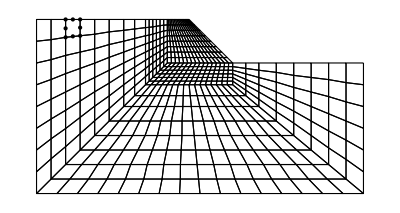

2

{1,2,5,12,17,26,35,48,64,79,100,123,149,178,209,243,278,319,381,466,563,668,803,950,1119,1278,1378,1435,1471,1501,1526,1550,1571}

{1571,1572,1574,1577,1579,1581,1586,1588,1591,1596,1599,1602,1605,1608,1610,1612,1613}

{1,3,6,13,18,29,39,55,70,91,112,139,170}

```mathematica
pack=Developer`ToPackedArray;
topol=pack@Transpose@Drop[Transpose@Import["https://www.dropbox.com/s/pyio7qkv52a6n60/mesh-talude-els.txt?dl=1","Table"],1];
nnodesAll=Import["https://www.dropbox.com/s/wkcyf51o1wppmpx/mesh-talude-nodes.txt?dl=1","Table"];
nnodes=pack@N[nnodesAll[[All,{2,3}]]];
allcoords=Table[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,8}];
(*edges are straight*)
meshVis1=Graphics[{FaceForm[],EdgeForm[Dashing[Tiny]],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];

meshVis2=Graphics[{FaceForm[],EdgeForm[Black],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{PointSize[Medium],Black,MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Black,Point[nnodes]}}];
meshVis1=Graphics[{FaceForm[],EdgeForm[Dashing[Tiny]],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
meshVis1=Graphics[{FaceForm[],EdgeForm[Black],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{PointSize[Medium],Black,MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Black,Point[nnodes]}}];
el=1;
nodeel=Table[nnodes[[topol[[el]][[i]]]],{i,1,Length[topol[[el]]]}]
nodeVis=Graphics[{PointSize[Medium],Black,{Black,Point[nodeel]}}];
Show[meshVis1,nodeVis]

order=2
serendipity=True;

x0=0.;xf=75;
y0=0;yf=0;
ndivs=10000;
searchpathinferiorline=Flatten[Table[{x,y},{x,x0,xf,(xf-x0)/ndivs},{y,y0,yf,(yf-y0)/ndivs}],1];
x0=0;xf=0.;
y0=0;yf=40;
searchpathleftline=Table[{x0,y},{y,y0,yf,(yf-y0)/ndivs}];
x0=75;xf=75;
y0=0;yf=30;
searchpathrigthline=Table[{x0,y},{y,y0,yf,(yf-y0)/ndivs}];
idsinferior=FindIds[nnodes,searchpathinferiorline]
idsleft=FindIds[nnodes,searchpathleftline]
idsrigth=FindIds[nnodes,searchpathrigthline]
```

```mathematica
planestress=False;
serendipity=True;
bodyforce=0;
order=2;
eltype=1;


(*subst2={c->50.,phi->20/180. Pi,young->20000. (*kPa*),nu->0.49,G->young/(2(1+nu)),K->(young)/(3 (1-2nu)),A->3 Tan[phi]/Sqrt[9+12 Tan[phi]^2],
B->3 /Sqrt[9+12 Tan[phi]^2]};*)

subst2={young->20000, nu->0.49,G->young/(2(1+nu)),K->(young)/(3 (1-2nu)),a->(c/(Sqrt[3] Tan[phi])-apex),b->a tanphi,apex->c Cot[phi] ,phi->Pi/9.,c->50.,tanphi->-(3 Tan[phi])/Sqrt[9+12 Tan[phi]^2]};
f[x_]:=0;
(*FEXT=ContributeStraigthLineNewman[nnodes,order,idssup,{0,-1},f];*)
bodyforce=20;


globalcounter=1;
intrule=IntegrationRule[order,eltype];
npts=Length[intrule]; 
nglobalpts=Length[topol] npts;
epspvec=Table[0,{nglobalpts},{3}];
epspsolitern=Table[0,{nglobalpts},{3}];

solss={};
sol2={{0,0}};
sol3={};
displace=Table[0,{Length[nnodes] 2}];
AppendTo[solss,displace];
epspsolu={};
stresssolu={};
dgammasol={};
soltalude={};
lamb=1;
diff=10;
l0=5;
l=l0
niterdesired=5;
counterout=1;
tol1=10^-6;
tol2=10^-6;
While[Abs[diff]>tol1 && counterout≤8,

Print["i = ",counterout, " | lamb = ",lamb, " | lambn = ",lambn," | diff = ",diff];
counter=1;
err1=10;
err2=10;

dw=Table[0,{Length[nnodes] 2}];

lambn=lamb;
While[counter≤10&& err2>tol2,

epsppost={};
dgamma={};
stressppost={};
globalcounter=1;
{KT,FINT,FEXTB}=Assemble[allcoords,nnodes,topol,order,eltype,displace];
FEXT=FEXTB;
imposex=1;
imposey=2;
R=lamb  FEXT-FINT;
{KT,R}=ContributeLineDirichlet[KT,R,idsinferior,{imposey,0}];
{KT,R}=ContributeLineDirichlet[KT,R,idsleft,{imposex,0}];
{KT,R}=ContributeLineDirichlet[KT,R,idsrigth,{imposex,0}];

{KT,FEXT}=ContributeLineDirichlet[KT,FEXT,idsinferior,{imposey,0}];
{KT,FEXT}=ContributeLineDirichlet[KT,FEXT,idsleft,{imposex,0}];
{KT,FEXT}=ContributeLineDirichlet[KT,FEXT,idsrigth,{imposex,0}];

dws=LinearSolve[KT,R,Method->"Banded"];
dwb=LinearSolve[KT,FEXT,Method->"Banded"];;
aa=dwb.dwb;
bb=2(dw+dws).dwb;
ccc=(dw+dws).(dw+dws)-l^2;
(*Print["a = ",aa];
Print["b = ",bb];
Print["c = ",ccc];*)
dlamb=Solve[aa x^2 +bb x+ccc==0,x][[2,1,2]];
dww=dws+dlamb dwb;
dw+=dww;
lamb+=dlamb;
(*dw=LinearSolve[KT,R];*)
res=Norm[dww];
displace+=dww;
err1=Norm[R]/Norm[lamb  FEXT];
(*If[err1>temp && counter>4,diverge=True];*)
temp=err1;
err2=Norm[dww]/Norm[displace];

Print["Iteration number = " ,counter,"  |R|/|FE| =  ",Norm[R]/Norm[lamb FEXT], "  |Δu|/|u| = ",Norm[dww]/Norm[displace],"  |R| =  ",Norm[R] , " |dw| = ",Norm[dww], " | dlamb = ",dlamb, " | lamb = ",lamb, " | bodyforce lamb = ",bodyforce lamb];
counter++;
];
diff=Abs[lamb-lambn];
Print["l = ",l];
AppendTo[stresssolu,stressppost];
AppendTo[dgammasol,dgamma];
AppendTo[epspsolu,epsppost];
AppendTo[solss,displace];
id=FindIds[nnodes,{{35,40}}][[1]];
AppendTo[soltalude,{-displace[[id 2]], lamb}];
AppendTo[sol3,epspvec];

(*Atualiza variável de estado plástica no passo convergido*)
epspsolitern=epspvec;
counterout++;
]
```

5

i = 1 | lamb = 1 | lambn = 0.945172 | diff = 10

Iteration number = 1  |R|/|FE| =  0.917139  |Δu|/|u| = 1.  |R| =  3252.58 |dw| = 5. | dlamb = 0.0903476 | lamb = 1.09035 | bodyforce lamb = 21.807

Iteration number = 2  |R|/|FE| =  0.024479  |Δu|/|u| = 0.000266521  |R| =  86.8035 |dw| = 0.0013326 | dlamb = -0.00012616 | lamb = 1.09022 | bodyforce lamb = 21.8044

Iteration number = 3  |R|/|FE| =  0.00919747  |Δu|/|u| = 0.000260795  |R| =  32.6111 |dw| = 0.00130397 | dlamb = -0.000114518 | lamb = 1.09011 | bodyforce lamb = 21.8021

Iteration number = 4  |R|/|FE| =  0.00449089  |Δu|/|u| = 0.00013323  |R| =  15.9224 |dw| = 0.000666152 | dlamb = -0.0000565435 | lamb = 1.09005 | bodyforce lamb = 21.801

Iteration number = 5  |R|/|FE| =  0.000108099  |Δu|/|u| = 2.02349×10^-6  |R| =  0.383264 |dw| = 0.0000101174 | dlamb = -8.5231×10^-7 | lamb = 1.09005 | bodyforce lamb = 21.801

Iteration number = 6  |R|/|FE| =  1.27613×10^-8  |Δu|/|u| = 3.93488×10^-10  |R| =  0.0000452448 |dw| = 1.96744×10^-9 | dlamb = -1.61637×10^-10 | lamb = 1.09005 | bodyforce lamb = 21.801

l = 5

i = 2 | lamb = 1.09005 | lambn = 1 | diff = 0.0900495

Iteration number = 1  |R|/|FE| =  0.000491987  |Δu|/|u| = 0.500001  |R| =  3.4859 |dw| = 5. | dlamb = 1.08833 | lamb = 2.17838 | bodyforce lamb = 43.5675

Iteration number = 2  |R|/|FE| =  0.0503984  |Δu|/|u| = 0.00455493  |R| =  356.213 |dw| = 0.0455484 | dlamb = -0.00535169 | lamb = 2.17303 | bodyforce lamb = 43.4605

Iteration number = 3  |R|/|FE| =  0.0341425  |Δu|/|u| = 0.00261046  |R| =  240.999 |dw| = 0.0261036 | dlamb = -0.00286405 | lamb = 2.17016 | bodyforce lamb = 43.4032

Iteration number = 4  |R|/|FE| =  0.020715  |Δu|/|u| = 0.00137544  |R| =  146.121 |dw| = 0.0137537 | dlamb = -0.00145816 | lamb = 2.1687 | bodyforce lamb = 43.3741

Iteration number = 5  |R|/|FE| =  0.00666671  |Δu|/|u| = 0.000297003  |R| =  47.0197 |dw| = 0.00296987 | dlamb = -0.000304603 | lamb = 2.1684 | bodyforce lamb = 43.368

Iteration number = 6  |R|/|FE| =  0.00152261  |Δu|/|u| = 0.0000279392  |R| =  10.7387 |dw| = 0.000279377 | dlamb = -0.0000319694 | lamb = 2.16837 | bodyforce lamb = 43.3673

Iteration number = 7  |R|/|FE| =  0.000170665  |Δu|/|u| = 2.15969×10^-6  |R| =  1.20367 |dw| = 0.0000215957 | dlamb = -1.54524×10^-6 | lamb = 2.16836 | bodyforce lamb = 43.3673

Iteration number = 8  |R|/|FE| =  6.46164×10^-7  |Δu|/|u| = 3.27393×10^-9  |R| =  0.00455726 |dw| = 3.27375×10^-8 | dlamb = -2.33268×10^-9 | lamb = 2.16836 | bodyforce lamb = 43.3673

l = 5

i = 3 | lamb = 2.16836 | lambn = 1.09005 | diff = 1.07832

Iteration number = 1  |R|/|FE| =  0.00153997  |Δu|/|u| = 0.333367  |R| =  16.2148 |dw| = 5. | dlamb = 1.06883 | lamb = 3.2372 | bodyforce lamb = 64.744

Iteration number = 2  |R|/|FE| =  0.0509735  |Δu|/|u| = 0.00887132  |R| =  533.218 |dw| = 0.133028 | dlamb = -0.0210804 | lamb = 3.21612 | bodyforce lamb = 64.3224

Iteration number = 3  |R|/|FE| =  0.0233706  |Δu|/|u| = 0.0032405  |R| =  243.982 |dw| = 0.0485871 | dlamb = -0.00644813 | lamb = 3.20967 | bodyforce lamb = 64.1934

Iteration number = 4  |R|/|FE| =  0.0137965  |Δu|/|u| = 0.00127219  |R| =  143.947 |dw| = 0.0190739 | dlamb = -0.00189114 | lamb = 3.20778 | bodyforce lamb = 64.1556

Iteration number = 5  |R|/|FE| =  0.00635982  |Δu|/|u| = 0.0004428  |R| =  66.3442 |dw| = 0.00663882 | dlamb = -0.000548082 | lamb = 3.20723 | bodyforce lamb = 64.1446

Iteration number = 6  |R|/|FE| =  0.00368331  |Δu|/|u| = 0.000151031  |R| =  38.4213 |dw| = 0.00226437 | dlamb = -0.000182836 | lamb = 3.20705 | bodyforce lamb = 64.1409

Iteration number = 7  |R|/|FE| =  0.001009  |Δu|/|u| = 0.0000291565  |R| =  10.525 |dw| = 0.000437135 | dlamb = -0.0000313145 | lamb = 3.20702 | bodyforce lamb = 64.1403

Iteration number = 8  |R|/|FE| =  0.00011945  |Δu|/|u| = 3.19127×10^-6  |R| =  1.246 |dw| = 0.0000478458 | dlamb = -3.42824×10^-6 | lamb = 3.20701 | bodyforce lamb = 64.1403

Iteration number = 9  |R|/|FE| =  0.000014465  |Δu|/|u| = 1.77991×10^-7  |R| =  0.150886 |dw| = 2.66857×10^-6 | dlamb = -1.84514×10^-7 | lamb = 3.20701 | bodyforce lamb = 64.1402

l = 5

i = 4 | lamb = 3.20701 | lambn = 2.16836 | diff = 1.03865

Iteration number = 1  |R|/|FE| =  0.0031554  |Δu|/|u| = 0.250152  |R| =  43.4862 |dw| = 5. | dlamb = 1.03009 | lamb = 4.2371 | bodyforce lamb = 84.742

Iteration number = 2  |R|/|FE| =  0.0324594  |Δu|/|u| = 0.0167958  |R| =  443.291 |dw| = 0.335364 | dlamb = -0.0383472 | lamb = 4.19875 | bodyforce lamb = 83.9751

Iteration number = 3  |R|/|FE| =  0.0272412  |Δu|/|u| = 0.00941021  |R| =  370.323 |dw| = 0.187727 | dlamb = -0.0192471 | lamb = 4.17951 | bodyforce lamb = 83.5901

Iteration number = 4  |R|/|FE| =  0.0148948  |Δu|/|u| = 0.00656973  |R| =  201.86 |dw| = 0.130963 | dlamb = -0.0128486 | lamb = 4.16666 | bodyforce lamb = 83.3331

Iteration number = 5  |R|/|FE| =  0.0129142  |Δu|/|u| = 0.0103821  |R| =  174.19 |dw| = 0.206666 | dlamb = -0.0197335 | lamb = 4.14692 | bodyforce lamb = 82.9385

Iteration number = 6  |R|/|FE| =  0.0100708  |Δu|/|u| = 0.0101359  |R| =  135.173 |dw| = 0.201429 | dlamb = -0.0202967 | lamb = 4.12663 | bodyforce lamb = 82.5325

Iteration number = 7  |R|/|FE| =  0.00576164  |Δu|/|u| = 0.0041359  |R| =  77.1807 |dw| = 0.0821312 | dlamb = -0.00816864 | lamb = 4.11846 | bodyforce lamb = 82.3692

Iteration number = 8  |R|/|FE| =  0.00315205  |Δu|/|u| = 0.00194762  |R| =  42.1908 |dw| = 0.0386642 | dlamb = -0.00320642 | lamb = 4.11525 | bodyforce lamb = 82.305

Iteration number = 9  |R|/|FE| =  0.00212392  |Δu|/|u| = 0.000937784  |R| =  28.4172 |dw| = 0.0186138 | dlamb = -0.00171616 | lamb = 4.11354 | bodyforce lamb = 82.2707

Iteration number = 10  |R|/|FE| =  0.000563702  |Δu|/|u| = 0.000233193  |R| =  7.5413 |dw| = 0.00462837 | dlamb = -0.0004455 | lamb = 4.11309 | bodyforce lamb = 82.2618

l = 5

i = 5 | lamb = 4.11309 | lambn = 3.20701 | diff = 0.906078

Iteration number = 1  |R|/|FE| =  0.0387213  |Δu|/|u| = 0.201276  |R| =  643.12 |dw| = 5. | dlamb = 0.993289 | lamb = 5.10638 | bodyforce lamb = 102.128

Iteration number = 2  |R|/|FE| =  0.0336619  |Δu|/|u| = 0.117303  |R| =  515.446 |dw| = 2.82513 | dlamb = -0.398609 | lamb = 4.70777 | bodyforce lamb = 94.1554

Iteration number = 3  |R|/|FE| =  0.0944549  |Δu|/|u| = 0.104954  |R| =  1305.58 |dw| = 2.36899 | dlamb = -0.458131 | lamb = 4.24964 | bodyforce lamb = 84.9928

Iteration number = 4  |R|/|FE| =  0.0851458  |Δu|/|u| = 0.0115718  |R| =  1163.3 |dw| = 0.25904 | dlamb = -0.0491491 | lamb = 4.20049 | bodyforce lamb = 84.0098

Iteration number = 5  |R|/|FE| =  0.0270913  |Δu|/|u| = 0.00457473  |R| =  368.91 |dw| = 0.102182 | dlamb = -0.0138879 | lamb = 4.1866 | bodyforce lamb = 83.7321

Iteration number = 6  |R|/|FE| =  0.00652074  |Δu|/|u| = 0.00295049  |R| =  88.6976 |dw| = 0.0658532 | dlamb = -0.00457707 | lamb = 4.18203 | bodyforce lamb = 83.6405

Iteration number = 7  |R|/|FE| =  0.00350684  |Δu|/|u| = 0.00175305  |R| =  47.667 |dw| = 0.0391052 | dlamb = -0.00301542 | lamb = 4.17901 | bodyforce lamb = 83.5802

Iteration number = 8  |R|/|FE| =  0.00153107  |Δu|/|u| = 0.000622118  |R| =  20.8077 |dw| = 0.0138756 | dlamb = -0.00070315 | lamb = 4.17831 | bodyforce lamb = 83.5662

Iteration number = 9  |R|/|FE| =  0.000348959  |Δu|/|u| = 0.0000867684  |R| =  4.74239 |dw| = 0.00193523 | dlamb = -0.0000634265 | lamb = 4.17824 | bodyforce lamb = 83.5649

Iteration number = 10  |R|/|FE| =  0.000318455  |Δu|/|u| = 3.90744×10^-6  |R| =  4.32783 |dw| = 0.0000871492 | dlamb = -1.81514×10^-6 | lamb = 4.17824 | bodyforce lamb = 83.5648

l = 5

i = 6 | lamb = 4.17824 | lambn = 4.11309 | diff = 0.065152

Iteration number = 1  |R|/|FE| =  0.00238509  |Δu|/|u| = 0.1833  |R| =  39.9877 |dw| = 5. | dlamb = 0.97634 | lamb = 5.15458 | bodyforce lamb = 103.092

Iteration number = 2  |R|/|FE| =  0.0250939  |Δu|/|u| = 0.158617  |R| =  363.545 |dw| = 4.15276 | dlamb = -0.700458 | lamb = 4.45412 | bodyforce lamb = 89.0825

Iteration number = 3  |R|/|FE| =  0.027085  |Δu|/|u| = 0.0494351  |R| =  371.112 |dw| = 1.25524 | dlamb = -0.241545 | lamb = 4.21258 | bodyforce lamb = 84.2516

Iteration number = 4  |R|/|FE| =  0.0377465  |Δu|/|u| = 0.00412013  |R| =  515.685 |dw| = 0.104464 | dlamb = -0.0122957 | lamb = 4.20028 | bodyforce lamb = 84.0057

Iteration number = 5  |R|/|FE| =  0.0109325  |Δu|/|u| = 0.00359429  |R| =  149.179 |dw| = 0.0910845 | dlamb = -0.00501244 | lamb = 4.19527 | bodyforce lamb = 83.9054

Iteration number = 6  |R|/|FE| =  0.00483407  |Δu|/|u| = 0.00318049  |R| =  65.9147 |dw| = 0.0805623 | dlamb = -0.00307685 | lamb = 4.19219 | bodyforce lamb = 83.8439

Iteration number = 7  |R|/|FE| =  0.00162951  |Δu|/|u| = 0.0011982  |R| =  22.2103 |dw| = 0.0303427 | dlamb = -0.00166773 | lamb = 4.19053 | bodyforce lamb = 83.8105

Iteration number = 8  |R|/|FE| =  0.000959384  |Δu|/|u| = 0.000421144  |R| =  13.0749 |dw| = 0.0106641 | dlamb = -0.000509017 | lamb = 4.19002 | bodyforce lamb = 83.8003

Iteration number = 9  |R|/|FE| =  0.000700236  |Δu|/|u| = 0.000435414  |R| =  9.54271 |dw| = 0.0110251 | dlamb = -0.000165843 | lamb = 4.18985 | bodyforce lamb = 83.797

Iteration number = 10  |R|/|FE| =  0.000368057  |Δu|/|u| = 0.000196743  |R| =  5.01573 |dw| = 0.00498166 | dlamb = -0.0000723474 | lamb = 4.18978 | bodyforce lamb = 83.7956

l = 5

i = 7 | lamb = 4.18978 | lambn = 4.17824 | diff = 0.0115364

Iteration number = 1  |R|/|FE| =  0.0807872  |Δu|/|u| = 0.166467  |R| =  1371.8 |dw| = 5. | dlamb = 1.0308 | lamb = 5.22058 | bodyforce lamb = 104.412

Iteration number = 2  |R|/|FE| =  0.0498998  |Δu|/|u| = 0.0827242  |R| =  795.405 |dw| = 2.50377 | dlamb = -0.319851 | lamb = 4.90073 | bodyforce lamb = 98.0146

Iteration number = 3  |R|/|FE| =  0.0815008  |Δu|/|u| = 0.0957161  |R| =  1157.76 |dw| = 2.80364 | dlamb = -0.533273 | lamb = 4.36746 | bodyforce lamb = 87.3492

Iteration number = 4  |R|/|FE| =  0.0746501  |Δu|/|u| = 0.0171543  |R| =  1039.53 |dw| = 0.498724 | dlamb = -0.086119 | lamb = 4.28134 | bodyforce lamb = 85.6268

Iteration number = 5  |R|/|FE| =  0.0324216  |Δu|/|u| = 0.009697  |R| =  446.489 |dw| = 0.280734 | dlamb = -0.0473755 | lamb = 4.23396 | bodyforce lamb = 84.6793

Iteration number = 6  |R|/|FE| =  0.0143615  |Δu|/|u| = 0.00475536  |R| =  196.806 |dw| = 0.13743 | dlamb = -0.0207866 | lamb = 4.21318 | bodyforce lamb = 84.2636

Iteration number = 7  |R|/|FE| =  0.0352398  |Δu|/|u| = 0.00578258  |R| =  481.769 |dw| = 0.167039 | dlamb = -0.0100064 | lamb = 4.20317 | bodyforce lamb = 84.0634

Iteration number = 8  |R|/|FE| =  0.0141308  |Δu|/|u| = 0.00268079  |R| =  192.929 |dw| = 0.0774152 | dlamb = -0.0055535 | lamb = 4.19762 | bodyforce lamb = 83.9524

Iteration number = 9  |R|/|FE| =  0.00436282  |Δu|/|u| = 0.000687518  |R| =  59.5458 |dw| = 0.0198522 | dlamb = -0.00141854 | lamb = 4.1962 | bodyforce lamb = 83.924

Iteration number = 10  |R|/|FE| =  0.00157957  |Δu|/|u| = 0.000873371  |R| =  21.5562 |dw| = 0.0252173 | dlamb = -0.00048217 | lamb = 4.19572 | bodyforce lamb = 83.9143

l = 5

i = 8 | lamb = 4.19572 | lambn = 4.18978 | diff = 0.00593828

Iteration number = 1  |R|/|FE| =  0.386811  |Δu|/|u| = 0.150106  |R| =  6613.64 |dw| = 5. | dlamb = 1.06097 | lamb = 5.25669 | bodyforce lamb = 105.134

Iteration number = 2  |R|/|FE| =  0.0589202  |Δu|/|u| = 0.0698692  |R| =  949.448 |dw| = 2.36368 | dlamb = -0.302441 | lamb = 4.95425 | bodyforce lamb = 99.085

Iteration number = 3  |R|/|FE| =  0.0770625  |Δu|/|u| = 0.0792127  |R| =  1118.53 |dw| = 2.63684 | dlamb = -0.491765 | lamb = 4.46248 | bodyforce lamb = 89.2497

Iteration number = 4  |R|/|FE| =  0.0582667  |Δu|/|u| = 0.0189365  |R| =  821.494 |dw| = 0.625445 | dlamb = -0.127818 | lamb = 4.33467 | bodyforce lamb = 86.6933

Iteration number = 5  |R|/|FE| =  0.0346241  |Δu|/|u| = 0.0117778  |R| =  481.423 |dw| = 0.387723 | dlamb = -0.0598271 | lamb = 4.27484 | bodyforce lamb = 85.4968

Iteration number = 6  |R|/|FE| =  0.0890978  |Δu|/|u| = 0.0121347  |R| =  1227.51 |dw| = 0.39871 | dlamb = -0.0390838 | lamb = 4.23575 | bodyforce lamb = 84.7151

Iteration number = 7  |R|/|FE| =  0.0229962  |Δu|/|u| = 0.00703442  |R| =  314.944 |dw| = 0.23078 | dlamb = -0.0251111 | lamb = 4.21064 | bodyforce lamb = 84.2129

Iteration number = 8  |R|/|FE| =  0.0116483  |Δu|/|u| = 0.00292077  |R| =  159.171 |dw| = 0.0957733 | dlamb = -0.0094449 | lamb = 4.2012 | bodyforce lamb = 84.024

Iteration number = 9  |R|/|FE| =  0.00915931  |Δu|/|u| = 0.00208148  |R| =  125.09 |dw| = 0.068255 | dlamb = -0.00233138 | lamb = 4.19887 | bodyforce lamb = 83.9773

Iteration number = 10  |R|/|FE| =  0.00233995  |Δu|/|u| = 0.000843448  |R| =  31.9516 |dw| = 0.0276591 | dlamb = -0.0007223 | lamb = 4.19814 | bodyforce lamb = 83.9629

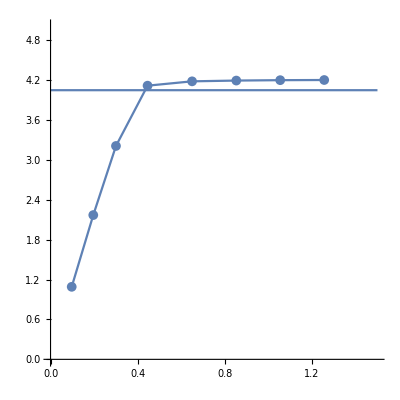

```mathematica
Show[ListLinePlot[soltalude,AspectRatio->1,PlotMarkers->{Automatic, 10}],Plot[4.045,{x,0,1.5}],PlotRange->{{0,1.5},{0,5}}]
```

```mathematica
soltalude[[4]]
```

{0.445166,4.11309}

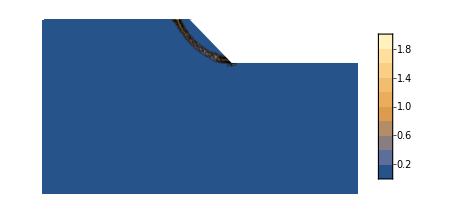

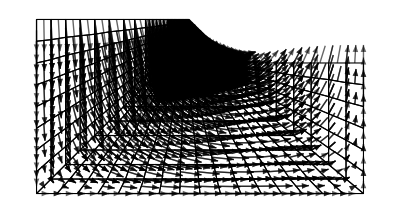

```mathematica
solnumber=5;
sol=solss[[solnumber]];
scale=10;
(*deformed=(Flatten[nnodes]+scale sol);

g=Show[meshVis1,Graphics[{FaceForm[],EdgeForm[Black],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3,4}]]]]}]]*)
gph=Graphics[{White,Polygon[{{35,40},{45,30},{75,30},{75,40}}]}];
{vecs2,vecs3}=ComputeSolNoInterpolation[topol,nnodes,order,sol,eltype,scale];
arrows=Table[Graphics[{Opacity[0.6],Black,Arrowheads[.007],Arrow[{vecs2[[el]][[i]][[1]],vecs2[[el]][[i]][[2]]}]}],{el,1,Length[vecs2]},{i,1,Length[vecs2[[el]]]}];
teste1=Table[{dgammasol[[solnumber]][[i]][[1]],dgammasol[[solnumber]][[i]][[2]],dgammasol[[solnumber]][[i]][[3]]},{i,1,Length[dgammasol[[solnumber]]]}];
labels=Range[0.,0.2,0.25];
(*plot=ListContourPlot[teste1,PlotLegends->{Placed[BarLegend[Automatic,8],{Left,Center}]},InterpolationOrder->20,PlotRange->All,LabelStyle->{Black,FontSize->50}];
Show[plot,gph,AspectRatio->Automatic,Frame->False,BaseStyle->{FontSize->20,FontFamily->"Helvetica",Black}]*)

plot=ListContourPlot[teste1,InterpolationOrder->20,PlotRange->All,LabelStyle->{Black,FontSize->12},PlotLegends->Automatic];
Show[plot,gph,AspectRatio->Automatic,Frame->False,BaseStyle->{FontSize->20,FontFamily->"Helvetica",Black}]

sh=Show[meshVis1,arrows,PlotRange->All]
```